# ODE simulation RESEAU BOOLEEN VERLINGUE 2016 -- T2DM VARIANT

```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
<< BooleanToLogisticODE`
```

```mathematica
Unprotect[t]; Clear[t]; Protect[t];
```

## RESEAU BOOLEEN VERLINGUE 2016 -- T2DM VARIANT

Etape 1 -- Regles exactement telles que publiees. FBraw reprend, noeud par noeud, la forme AND-de-OR / OR-de-AND curatee depuis la litterature dans le modele SBML-qual original (avant toute reduction). Cette forme n'est PAS en DNF minimale : Senescence par exemple est ecrite (mTORC1_S6K1 || p16) && (p16 || p21), alors que sa DNF minimale est (mTORC1_S6K1 && p21) || p16. Garder la forme brute rend la provenance directement tracable au papier (Verlingue et al. 2016, Aging Cell 15:1018-1026). Les noms composes mTORC1_S6K1, G1_S, IRS_PIK3CA utilisent   au lieu de _, reserve comme Blank en Wolfram Language.

```mathematica
FBraw = {
 Insulin -> True,
 GF -> True,
 Therapy -> True,
 Senescence -> (mTORC1 S6K1 || p16) && (p16 || p21),
 G1 S -> CDK2 && E2F1 && Metabolism && !p21,
 MAPK -> GF && !PP2A,
 p16 -> !E2F1 && MAPK && !p53 && !PRC,
 MDM2 -> (AKT || p16 || p53) && !E2F1 && !mTORC1 S6K1 && !MYC,
 p53 -> !MDM2,
 p21 -> !AKT && (FOXO || p53) && !MYC,
 AKT -> (CDK2 || IRS PIK3CA) && !PP2A && !PTEN,
 mTORC1 S6K1 -> !AMPK && !TSC,
 ATP -> Metabolism,
 IRS PIK3CA -> Insulin && !mTORC1 S6K1,
 AMPK -> !ATP && p53,
 PTEN -> !AKT && p53,
 TSC -> !AKT && AMPK && !MAPK,
 MYC -> E2F1 && MAPK && mTORC1 S6K1 && !p53,
 CDK2 -> (E2F1 || MYC) && mTORC1 S6K1 && !p21,
 pRB -> !CDK2,
 E2F1 -> E2F1 && (GF || MYC) && !pRB,
 PRC -> !AKT && MYC,
 Metabolism -> (AKT || PP1C) && (MAPK || mTORC1 S6K1),
 PP2A -> !mTORC1 S6K1,
 FOXO -> !AKT && (AMPK || Metabolism || p16) && !MAPK,
 PP1C -> AKT || MAPK
};
```

Etape 2 -- Suppression du noeud Therapy. Therapy est l'entree utilisee dans le papier UNIQUEMENT pour les simulations pharmacologiques (calibration des doses everolimus/rapamycine, Materials and Methods p.1024). Elle ne fait pas partie de la dynamique de base (Fig. 1 : noeud gris, distinct des entrees Insulin/GF). On la retire via DeleteCases.

```mathematica
FB = DeleteCases[FBraw, Therapy -> _];
```

Etape 3 -- Pourquoi BooleanMinimize est obligatoire.

```mathematica
FBmin = FB /. (lhs_ -> rhs_) :> (lhs -> BooleanMinimize[rhs, "DNF"])
```

{Insulin→True,GF→True,Senescence→(mTORC1 S6K1&&p21)||p16,G1 S→CDK2&&E2F1&&Metabolism&&!p21,MAPK→GF&&!PP2A,p16→!E2F1&&MAPK&&!p53&&!PRC,MDM2→(AKT&&!E2F1&&!mTORC1 S6K1&&!MYC)||(!E2F1&&!mTORC1 S6K1&&!MYC&&p16)||(!E2F1&&!mTORC1 S6K1&&!MYC&&p53),p53→!MDM2,p21→(!AKT&&FOXO&&!MYC)||(!AKT&&!MYC&&p53),AKT→(CDK2&&!PP2A&&!PTEN)||(IRS PIK3CA&&!PP2A&&!PTEN),mTORC1 S6K1→!AMPK&&!TSC,ATP→Metabolism,IRS PIK3CA→Insulin&&!mTORC1 S6K1,AMPK→!ATP&&p53,PTEN→!AKT&&p53,TSC→!AKT&&AMPK&&!MAPK,MYC→E2F1&&MAPK&&mTORC1 S6K1&&!p53,CDK2→(E2F1&&mTORC1 S6K1&&!p21)||(mTORC1 S6K1&&MYC&&!p21),pRB→!CDK2,E2F1→(E2F1&&GF&&!pRB)||(E2F1&&MYC&&!pRB),PRC→!AKT&&MYC,Metabolism→(AKT&&MAPK)||(AKT&&mTORC1 S6K1)||(MAPK&&PP1C)||(mTORC1 S6K1&&PP1C),PP2A→!mTORC1 S6K1,FOXO→(!AKT&&AMPK&&!MAPK)||(!AKT&&!MAPK&&Metabolism)||(!AKT&&!MAPK&&p16),PP1C→AKT||MAPK}

Etape 4 -- Parametres cinetiques : PAS issus du papier. Le papier utilise un modele booleen pur simule stochastiquement avec MaBoSS ("almost no parameters to tune", p.1019) : il n'y a pas de kappa/gamma/theta publies. La relaxation continue (ODE) est un choix de modelisation complementaire, pas une reproduction des Fig. 2/3 (probabilites MaBoSS). Les generateurs ci-dessous produisent un tirage dans les memes plages que le driver Traynard : kappa ~ Uniform[50,100], gamma ~ Uniform[0.25,2], theta ~ 15 + Uniform[-5,5] (donc Uniform[10,20], avec lambda=n/theta la pente du noyau), x0 ~ Uniform[0,100]. Ils sont donnes pour reference puis figes en associations litterales a la valeur reellement tiree, pour que le notebook soit reproductible. n=6 (coefficient de cooperativite, analogue au coefficient de Hill).

```mathematica
(* generateur de reference -- re-executer pour un nouveau tirage *)
κ = AssociationThread[Keys[FB], RandomReal[{50, 100}, Length[Keys[FB]]]];
```

```mathematica
κ = <|
  Insulin -> 57.02,
  GF -> 54.56,
  Senescence -> 64.41,
  G1 S -> 98.91,
  MAPK -> 66.49,
  p16 -> 99.45,
  MDM2 -> 80.8,
  p53 -> 54.35,
  p21 -> 71.1,
  AKT -> 90.84,
  mTORC1 S6K1 -> 55.85,
  ATP -> 63.22,
  IRS PIK3CA -> 54.26,
  AMPK -> 64.52,
  PTEN -> 68.46,
  TSC -> 50.06,
  MYC -> 83.54,
  CDK2 -> 55.61,
  pRB -> 59.77,
  E2F1 -> 76.8,
  PRC -> 57.57,
  Metabolism -> 94.12,
  PP2A -> 87.84,
  FOXO -> 97.44,
  PP1C -> 71.26
|>;
```

```mathematica
(* generateur de reference *)
γ = AssociationThread[Keys[FB], RandomReal[{0.25, 2}, Length[Keys[FB]]]];
```

```mathematica
γ = <|
  Insulin -> 1.84,
  GF -> 1.96,
  Senescence -> 1.89,
  G1 S -> 1.17,
  MAPK -> 1.22,
  p16 -> 1.26,
  MDM2 -> 1.89,
  p53 -> 0.72,
  p21 -> 0.6,
  AKT -> 0.5,
  mTORC1 S6K1 -> 0.48,
  ATP -> 1.44,
  IRS PIK3CA -> 1.8,
  AMPK -> 1.34,
  PTEN -> 1.8,
  TSC -> 1.48,
  MYC -> 0.99,
  CDK2 -> 0.34,
  pRB -> 0.59,
  E2F1 -> 1.26,
  PRC -> 1.75,
  Metabolism -> 0.43,
  PP2A -> 0.49,
  FOXO -> 1.2,
  PP1C -> 1.19
|>;
```

```mathematica
(* generateur de reference *)
θ = AssociationThread[Keys[FB], Array[15 + RandomReal[{-5, 5}] &, Length[Keys[FB]]]];
```

```mathematica
θ = <|
  Insulin -> 12.65,
  GF -> 15.85,
  Senescence -> 11.69,
  G1 S -> 10.61,
  MAPK -> 12.66,
  p16 -> 16.52,
  MDM2 -> 13.68,
  p53 -> 11.52,
  p21 -> 17.4,
  AKT -> 14.36,
  mTORC1 S6K1 -> 16.33,
  ATP -> 12.95,
  IRS PIK3CA -> 18.62,
  AMPK -> 17.48,
  PTEN -> 12.6,
  TSC -> 19.82,
  MYC -> 18.08,
  CDK2 -> 17.4,
  pRB -> 16.95,
  E2F1 -> 19.63,
  PRC -> 15.53,
  Metabolism -> 17.32,
  PP2A -> 12.05,
  FOXO -> 18.08,
  PP1C -> 16.38
|>;
```

```mathematica
n = 6;
```

```mathematica
(* generateur de reference *)
initialcondition = AssociationThread[Keys[FB], RandomReal[{0, 100}, Length[Keys[FB]]]];
```

```mathematica
initialcondition = <|
  Insulin -> 90.61,
  GF -> 41.06,
  Senescence -> 98.94,
  G1 S -> 2.4,
  MAPK -> 17.15,
  p16 -> 32.03,
  MDM2 -> 89.07,
  p53 -> 80.07,
  p21 -> 21.86,
  AKT -> 81.91,
  mTORC1 S6K1 -> 88.24,
  ATP -> 5.07,
  IRS PIK3CA -> 89.66,
  AMPK -> 48.06,
  PTEN -> 26.2,
  TSC -> 17.9,
  MYC -> 67.93,
  CDK2 -> 37.42,
  pRB -> 50.69,
  E2F1 -> 71.78,
  PRC -> 24.77,
  Metabolism -> 95.02,
  PP2A -> 92.73,
  FOXO -> 45.28,
  PP1C -> 75.96
|>;
```

```mathematica
(* arrondi propre a 0.01 des associations figees *)
κ = Round[#, 0.01] & /@ κ;
γ = Round[#, 0.01] & /@ γ;
θ = Round[#, 0.01] & /@ θ;
initialcondition = Round[#, 0.01] & /@ initialcondition;
```

#### ODE

Chaque gene i obeit a dx_i/dt = κ_i*Φ_i(x) - γ_i*x_i, ou Φ_i est le produit de noyaux logistiques obtenu en appliquant la formule de De Morgan a la regle DNF minimale de FBmin (BooleanToOdeSystem, package BooleanToLogisticODE`). fstep = {logisticm, logisticp} fournit les noyaux decroissant (repression) et croissant (activation). NDSolve integre de t=0 a t=60 depuis initialcondition, et le trace couvre le meme intervalle [0,60].

```mathematica
system1 = BooleanToOdeSystem[FBmin, t, κ, γ, θ, n,
   initialcondition, {logisticm, logisticp}];
```

```mathematica
Framed @ TableForm[system1]
```

Insulin'[t]==57.02-1.84 Insulin[t]
Insulin[0]==90.61
GF'[t]==54.56-1.96 GF[t]
GF[0]==41.06
Senescence'[t]==64.41 (1-logisticm[p16[t],16.52,6] (1-logisticp[mTORC1 S6K1[t],16.33,6] logisticp[p21[t],17.4,6]))-1.89 Senescence[t]
Senescence[0]==98.94
G1 S'[t]==-1.17 G1 S[t]+98.91 logisticm[p21[t],17.4,6] logisticp[CDK2[t],17.4,6] logisticp[E2F1[t],19.63,6] logisticp[Metabolism[t],17.32,6]
G1 S[0]==2.4
MAPK'[t]==66.49 logisticm[PP2A[t],12.05,6] logisticp[GF[t],15.85,6]-1.22 MAPK[t]
MAPK[0]==17.15
p16'[t]==99.45 logisticm[E2F1[t],19.63,6] logisticm[p53[t],11.52,6] logisticm[PRC[t],15.53,6] logisticp[MAPK[t],12.66,6]-1.26 p16[t]
p16[0]==32.03
MDM2'[t]==80.8 (1-(1-logisticm[E2F1[t],19.63,6] logisticm[mTORC1 S6K1[t],16.33,6] logisticm[MYC[t],18.08,6] logisticp[AKT[t],14.36,6]) (1-logisticm[E2F1[t],19.63,6] logisticm[mTORC1 S6K1[t],16.33,6] logisticm[MYC[t],18.08,6] logisticp[p16[t],16.52,6]) (1-logisticm[E2F1[t],19.63,6] logisticm[mTORC1 S6K1[t],16.33,6] logisticm[MYC[t],18.08,6] logisticp[p53[t],11.52,6]))-1.89 MDM2[t]
MDM2[0]==89.07
p53'[t]==54.35 logisticm[MDM2[t],13.68,6]-0.72 p53[t]
p53[0]==80.07
p21'[t]==71.1 (1-(1-logisticm[AKT[t],14.36,6] logisticm[MYC[t],18.08,6] logisticp[FOXO[t],18.08,6]) (1-logisticm[AKT[t],14.36,6] logisticm[MYC[t],18.08,6] logisticp[p53[t],11.52,6]))-0.6 p21[t]
p21[0]==21.86
AKT'[t]==-0.5 AKT[t]+90.84 (1-(1-logisticm[PP2A[t],12.05,6] logisticm[PTEN[t],12.6,6] logisticp[CDK2[t],17.4,6]) (1-logisticm[PP2A[t],12.05,6] logisticm[PTEN[t],12.6,6] logisticp[IRS PIK3CA[t],18.62,6]))
AKT[0]==81.91
mTORC1 S6K1'[t]==55.85 logisticm[AMPK[t],17.48,6] logisticm[TSC[t],19.82,6]-0.48 mTORC1 S6K1[t]
mTORC1 S6K1[0]==88.24
ATP'[t]==-1.44 ATP[t]+63.22 logisticp[Metabolism[t],17.32,6]
ATP[0]==5.07
IRS PIK3CA'[t]==-1.8 IRS PIK3CA[t]+54.26 logisticm[mTORC1 S6K1[t],16.33,6] logisticp[Insulin[t],12.65,6]
IRS PIK3CA[0]==89.66
AMPK'[t]==-1.34 AMPK[t]+64.52 logisticm[ATP[t],12.95,6] logisticp[p53[t],11.52,6]
AMPK[0]==48.06
PTEN'[t]==68.46 logisticm[AKT[t],14.36,6] logisticp[p53[t],11.52,6]-1.8 PTEN[t]
PTEN[0]==26.2
TSC'[t]==50.06 logisticm[AKT[t],14.36,6] logisticm[MAPK[t],12.66,6] logisticp[AMPK[t],17.48,6]-1.48 TSC[t]
TSC[0]==17.9
MYC'[t]==83.54 logisticm[p53[t],11.52,6] logisticp[E2F1[t],19.63,6] logisticp[MAPK[t],12.66,6] logisticp[mTORC1 S6K1[t],16.33,6]-0.99 MYC[t]
MYC[0]==67.93
CDK2'[t]==-0.34 CDK2[t]+55.61 (1-(1-logisticm[p21[t],17.4,6] logisticp[E2F1[t],19.63,6] logisticp[mTORC1 S6K1[t],16.33,6]) (1-logisticm[p21[t],17.4,6] logisticp[mTORC1 S6K1[t],16.33,6] logisticp[MYC[t],18.08,6]))
CDK2[0]==37.42
pRB'[t]==59.77 logisticm[CDK2[t],17.4,6]-0.59 pRB[t]
pRB[0]==50.69
E2F1'[t]==-1.26 E2F1[t]+76.8 (1-(1-logisticm[pRB[t],16.95,6] logisticp[E2F1[t],19.63,6] logisticp[GF[t],15.85,6]) (1-logisticm[pRB[t],16.95,6] logisticp[E2F1[t],19.63,6] logisticp[MYC[t],18.08,6]))
E2F1[0]==71.78
PRC'[t]==57.57 logisticm[AKT[t],14.36,6] logisticp[MYC[t],18.08,6]-1.75 PRC[t]
PRC[0]==24.77
Metabolism'[t]==94.12 (1-(1-logisticp[AKT[t],14.36,6] logisticp[MAPK[t],12.66,6]) (1-logisticp[AKT[t],14.36,6] logisticp[mTORC1 S6K1[t],16.33,6]) (1-logisticp[MAPK[t],12.66,6] logisticp[PP1C[t],16.38,6]) (1-logisticp[mTORC1 S6K1[t],16.33,6] logisticp[PP1C[t],16.38,6]))-0.43 Metabolism[t]
Metabolism[0]==95.02
PP2A'[t]==87.84 logisticm[mTORC1 S6K1[t],16.33,6]-0.49 PP2A[t]
PP2A[0]==92.73
FOXO'[t]==-1.2 FOXO[t]+97.44 (1-(1-logisticm[AKT[t],14.36,6] logisticm[MAPK[t],12.66,6] logisticp[AMPK[t],17.48,6]) (1-logisticm[AKT[t],14.36,6] logisticm[MAPK[t],12.66,6] logisticp[Metabolism[t],17.32,6]) (1-logisticm[AKT[t],14.36,6] logisticm[MAPK[t],12.66,6] logisticp[p16[t],16.52,6]))
FOXO[0]==45.28
PP1C'[t]==71.26 (1-logisticm[AKT[t],14.36,6] logisticm[MAPK[t],12.66,6])-1.19 PP1C[t]
PP1C[0]==75.96

```mathematica
fun = (#[t] &) /@ Keys[FB];
```

```mathematica
S = NDSolve[system1, Keys[FB], {t, 0, 60}, MaxSteps -> Infinity];
```

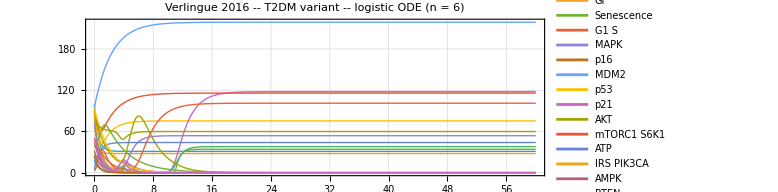

```mathematica
GG1 = Plot[Evaluate[fun /. S[[1]]], {t, 0, 60},
  PlotRange -> All, PlotTheme -> "Detailed", PlotStyle -> Thick,
  PlotLegends -> Placed[Keys[FB], Right],
  LabelStyle -> Directive[FontFamily -> "Franklin Gothic", 11],
  AspectRatio -> 1/3,
  PlotLabel -> "Verlingue 2016 -- T2DM variant -- logistic ODE (n = 6)",
  ImageSize -> Large]
```

#### Stable states (sanity check)

Un point fixe booleen (x = F(x)) correspond a un phenotype cellulaire stable au sens du papier : un attracteur vers lequel convergent les trajectoires MaBoSS. Verification INDEPENDANTE de l'integration ODE : elle porte sur FB (forme booleenne exacte, pre-minimisation, puisque x=F(x) ne depend pas de la syntaxe). Le reseau T2DM a exactement 2 points fixes (Insulin=GF=1 fixes), qui concordent noeud par noeud sur les 25 genes :
  - Etat proliferatif : E2F1=G1_S=CDK2=AKT=1, Senescence=p21=p16=0
  - Etat senescent : Senescence=p21=p53=PTEN=pRB=1, G1_S=E2F1=CDK2=0

```mathematica
stateProliferative = <|Insulin -> True, GF -> True, Senescence -> False,
   G1 S -> True, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> False, AKT -> True, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> False, AMPK -> False, PTEN -> False,
   TSC -> False, MYC -> False, CDK2 -> True, pRB -> False, E2F1 -> True,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

stateSenescent = <|Insulin -> True, GF -> True, Senescence -> True,
   G1 S -> False, MAPK -> True, p16 -> False, MDM2 -> False,
   p53 -> True, p21 -> True, AKT -> False, mTORC1 S6K1 -> True,
   ATP -> True, IRS PIK3CA -> False, AMPK -> False, PTEN -> True,
   TSC -> False, MYC -> False, CDK2 -> False, pRB -> True, E2F1 -> False,
   PRC -> False, Metabolism -> True, PP2A -> False, FOXO -> False, PP1C -> True|>;

checkFixedPoint[state_] := AllTrue[FB, (#[[1]] /. state) === (#[[2]] /. state) &]

{checkFixedPoint[stateProliferative], checkFixedPoint[stateSenescent]}
```

{True,True}

```mathematica
Export["VERLINGUE_T2DM_VARIANT.jpeg",GG1,ImageResolution->300]
```

VERLINGUE_T2DM_VARIANT.jpeg